Universidad de Jaén. EPS Jaén.
Departamento de Matemáticas. Grado en Ingeniería Informática
Análisis y Métodos Numéricos. 
F. Javier Muñoz Delgado

## Problemas de examen. Tema 5. Derivadas

### Cálculo de máximos y mínimos absolutos

## 6.- Calcular el máximo y mínimo absolutos de la función f(x)=3-|x-3|con x en [-1,5]. Octubre 22, Octubre 21

Solución:
La función f es una función continua (por ser composición de funciones continuas; polinomios y valor absoluto) y el dominio es un intervalo cerrado y acotado. Por tanto, el teorema de Weierstrass asegura que existe máximo y mínimo absolutos.
Para encontrarlos debemos estudiar los extremos del intervalo, los puntos con derivada 0 del interior del intervalo, y los puntos donde no exista derivada de la función.
La función valor absoluto es derivable en todo punto, excepto en el 0. El polinomio x-3 es cero en x=3.
Además,  x-3 es mayor que cero cuando x es mayor que 3. Por tanto,
f(x)=Piecewise[{{3-(x-3)=6-x, si x≥3.}, {3-(3-x)=x, si x ≤3.}}]
La derivada es -1 o 1, según el intervalo, y nunca se anularía.
Por tanto debemos estudiar el valor de f en los extremos (x=-1, x=5), en los puntos con derivada cero (ningún punto) y los puntos del interior sin derivada (x=3).
Evaluando f(-1)=-1, f(3)=3, f(5)=1.
El valor máximo de f es 3 que se alcanza en el punto x=3, el valor mínimo de f es -1, que se alcanza en el punto x=-1. 
Con e Mathematica podemos ver la gráfica de la función:

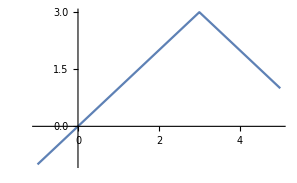

```mathematica
Plot[3-Abs[x-3],{x,-1,5}]
```

## 4.- Calcular los máximos y mínimos absolutos de la función f(x) =|x^2-1| en [-1, 3]. Julio 22

Solución:
La función f es una función continua (por ser composición de funciones continuas, primero un polinomio y luego el valor absoluto) y el dominio es un intervalo cerrado y acotado. Por tanto, el teorema de Weierstrass asegura que existe máximo y mínimo absolutos.
Para encontrarlos debemos estudiar los extremos del intervalo, los puntos con derivada 0 del interior del intervalo, y los puntos donde no exista derivada de la función.
La función valor absoluto es derivable en todo punto, excepto en el 0. Veamos cuando x^2-1 es cero.
x^2-1 = 0 ⟹ x = ±1. Además, x^2-1 es mayor que cero cuando x es menor que -1 o mayor que 1. Por tanto
f(x)=Piecewise[{{x^2-1, si x <-1 ó x >1}, {1-x^2, si -1≤x ≤1}}]
La derivada es 2x o -2x, según el intervalo, y que solo se anularía en x=0 .
Por tanto debemos estudiar el valor de f en los extremos (x=-1, x=3), en los puntos con derivada cero (x=0) y los puntos del interior sin derivada (x=1).
Evaluando f(-1)=0, f(0)=1, f(1)=0, f(3)=8.
El valor máximo de f es 8 que se alcanza en el punto x=3, el valor mínimo de f es 0, que se alcanza en los puntos x=-1 y x=1.

## 4.- Calcular los máximos y mínimos absolutos de la función f(x) =x^3-3 x^2+2 en el intervalo [1, 3]. Enero 22

Solución:
La función f(x) es una función continua por ser un polinomio (también es derivable por la misma razón). Al ser una función continua en un intervalo cerrado y acotado, el [1, 3], tiene máximo y mínimo absolutos.

Los máximos y mínimos absolutos se encuentran estudiando tres tipos de puntos:
a) Los extremos del intervalo. En este caso, x=1 y x=3.
b) Los puntos del interior del intervalo con derivada cero.
f’(x)= 3 x^2-6x
Calculamos cuándo 3 x^2-6x=0, y obtenemos 3 x^2-6x = 3x(x-2) =0. Será cierto cuando x=0 o x=2. El punto x=0, no está en el intervalo. Por tanto, solo consideramos x=2.
El único punto donde se anula la derivada en el intervalo es el punto x=2.
c) Los puntos donde no existe derivada. En este caso, la derivada existe en todos los puntos.

Basta ahora evaluar la función en los puntos que hemos encontrado:
	f(1)= 1^3-3*1^2+2= 0, 
	f(2)= 2^3-3*2^2+2= 8-12+2 = -2 , 
	f(3)= 3^3-3*3^2+2= 27-27+2=2

El valor máximo de la función es 2, que se alcanza en el punto x=3. El valor mínimo de la función es -2 que se alcanza en el punto x=2.
Si dibujamos la gráfica con el Mathematica vemos lo que ocurre con la función.

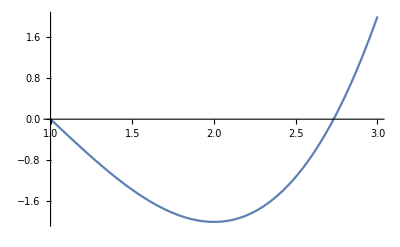

```mathematica
Plot[x^3-3 x^2+2,{x,1,3}]
```

## 4.- Calcular los máximos y mínimos absolutos de la función f(x) =|x^2-4| en el intervalo [-2,3]. Enero 21

Solución:
La función f(x) es una función continua por ser composición de funciones continuas, la función polinómica x^2-4 y la función valor absoluto. Al ser una función continua en un intervalo cerrado y acotado, el [-2,3], tiene máximo y mínimo absolutos.
Los máximos y mínimos absolutos se encuentran estudiando tres tipos de puntos:
a) Los extremos del intervalo. En este caso x=-2 y x=3.
b) Los puntos del interior del intervalo con derivada cero.
f(x)=Piecewise[{{x^2-4,, cuando x^2-4≥ 0}, {-(x^2-4),, cuando x^2-4≤ 0}}] 
Calculamos cuándo x^2-4=0, y obtenemos x=±2. Si x>2 o x<-2, x^2-4>0. En cambio, si -2<x<2, x^2-4<0. Por tanto,
f(x)=Piecewise[{{x^2-4,, si 2≤ x ≤ 3}, {-(x^2-4),, si -2≤x≤2}}] ⟹ f ‘(x)=Piecewise[{{2x,, si 2< x ≤ 3}, {-2x,, si -2≤x<2}}]
El único punto donde se anula la derivada es el punto x=0.
c) Los puntos donde no existe derivada. En este caso, en el punto x=2, que es donde cambia la definición de la función, pasando del polinomio -2x al polinomio 2x.
Basta ahora evaluar la función en los puntos que hemos encontrado en cada uno de los tipos de puntos.
f(-2)=|(-2)^2-4|=0, f(0)=|0^2-4|=4, f(2)=|2^2-4|=0, f(3)=|3^2-4|=5.
El valor máximo de la función es 5, que se alcanza en el punto x=3. El valor mínimo de la función es 0 que se alcanza en dos puntos, el punto x=-2 y el punto x=2.

Si dibujamos la gráfica con el Mathematica, obtenemos:

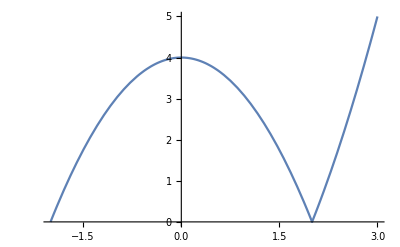

```mathematica
Plot[Abs[x^2-4],{x,-2,3}]
```

## 5.- Calcular el máximo y mínimo absolutos de la función f(x)=x^4-2 x^2 con x en el intervalo [-1/2, 2]. Enero 20

Solución:
Dado que es una función continua y derivable en un intervalo cerrado y acotado, tendrá máximo y mínimo absolutos, que alcanzará en los extremos del intervalo o en puntos con derivada cero (pues no hay puntos donde no exista la derivada).
	f’(x)= 4x^3 - 4 x =4x(x^2-1). 
La derivada se anula en 0 y 1 (también se anularía en -1, pero este punto no está en el intervalo).

Ahora, basta evaluar en los puntos de derivada 0 y en los extremos; 
	f(-1/2)= -7/16, 
	f(0)=0 ,
	f(1)=-1 ,
	f(2)=8. 
Por tanto el mínimo es -1, que se alcanza en el punto 1, y el máximo es 8, que se alcanza en el punto 2.

## 6.- Calcular el máximo y mínimo absolutos de la función f(x)=|4-x^2|con x en [-3,1]. Enero 2018

Solución:
La función f(x) es continua (por ser diferencia y composición de funciones continuas) y en el intervalo [-3,1] (cerrado y acotado) tiene máximo y mínimo absolutos (Teorema de Weierstrass). Para calcular el máximo y el mínimo absolutos calculamos los puntos que son candidatos: extremos del intervalo, puntos donde se anula la derivada, puntos donde la función no sea derivable.

f(x)=|4-x^2|=Piecewise[{{x^2-4,, cuando 4-x^2≤0⟺4 ⩽x^2⟺x≤-2 ó 2⩽x (en este caso,-3≤x≤-2)}, {4-x^2,, cuando4-x^2≥0⟺4 ≥x^2⟺-2≤x≤2 (en este caso,-2≤x≤1)}}] 

La derivada f ’(x)=
f ’(x)=Piecewise[{{2x,, cuando -3≤x<-2)}, {-2x,, cuando-2<x≤1)}}]

En el punto -2, la función no es derivable.

	1) Extremos: -3, 1.
	2) Puntos con derivada cero: 0.
	3) Puntos donde f no es derivable: -2.

Ahora evaluamos f en esos puntos
f(-3)= |4-(-3)^2|=5, f(1)=|4-1^2|=3, f(0)=|4-0^2|=4, f(-2)=|4-(-2)^2|=0.
Por tanto, el máximo está en el punto -3, donde la función vale 5 y el mínimo está en el punto -2, donde la función vale 0.

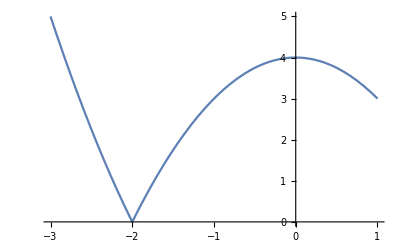

```mathematica
Plot[Abs[4-x^2],{x,-3,1}]
```

### Optimización

## 6.- Consideremos la figura formada por un rectángulo, de lados x (altura) y 2r (base), y un semicírculo de radio r. Si el perímetro de la figura resultante, L, está fijo, encontrar los valores de x y r para que el área sea máxima. Julio 23

Solución:
El área de la figura es x*2r+(π  r^2)/2. El perímetro es 2x+2r+π*r =L. Despejando x=(L-2r-π*r)/2 y sustituyendo en el área   x*2r+(π  r^2)/2 = (L-2r-π*r)r+(π  r^2)/2=  L*r-2 r^2-(π  r^2)/2 =A(r).
Como x y r no pueden ser negativos, 2x=L-r(2+π)≥0, r≤L/(2+π). Por tanto debemos buscar el máximo de A(r)=L*r-2 r^2-(π  r^2)/2  en el intervalo [0,L/(2+π)]. 
Es una función polinómica de grado dos con coeficiente líder negativo, es continua y derivable en el intervalo. Tendrá por tanto máximo y mínimo absoluto. 
A’(r)=L-4r-π  r = 0 ⟹ r=L/(4+π)
Evaluamos A en los extremos del intervalo y donde se anula la derivada:
A(0)=L*0-2*0^2-(π*0^2)/2=0
A(L/(4+π))= L*L/(4+π)-2(L/(4+π))^2-(π (L/(4+π))^2)/2 =L^2/(4+π)-(2 L^2)/(4+π)^2-(π L^2)/(2(4+π)^2)=L^2/(2(4+π))(2-4/(4+π)-π/(4+π))=L^2/(2(4+π))
A(L/(2+π))=L*L/(2+π)-2(L/(2+π))^2-(π (L/(2+π))^2)/2=L^2/(2+π)-(2 L^2)/(2+π)^2-(π L^2)/(2(2+π)^2)=L^2/(2(2+π))(2-4/(2+π)-π/(2+π))=L^2/(2(2+π))((4+2π-4-π)/(2+π))=L^2/(2(2+π))(π/(2+π)) 

Comparamos  L^2/(2(4+π)) con L^2/(2(2+π))(π/(2+π)). Simplificando L^2/2 en las dos expresiones, tenemos 1/(4+π) y 1/(2+π)(π/(2+π)) . Multiplicando por (4+π) (2+π)^2, tenemos (2+π)^2= (4+4π+π^2) y π(4+π)=(4π+π^2). Por tanto, la primera expresión es la mayor. También, se puede razonar considerando que la función es un polinomio de grado dos y coeficiente líder negativo, lo que hace que en el punto donde se anula la derivada se tiene un máximo absoluto. 

El máximo se consigue en r=L/(4+π). El valor de x será x= (L-2r-π*r)/2 = (L-(2+π)*r)/2=(L-(2+π)*(L/(4+π)))/2=L/2(1-((2+π)/(4+π)))=L/2(2/(4+π))=L/(4+π)

(En este caso, considerando que la función A(r) es polinómica de grado dos y con coeficiente líder negativo, podríamos razonar que en todo ℝ tiene máximo absoluto y no tiene mínimo absoluto. Como A’(r) se anula en el punto  r=L/(4+π), tenemos que el máximo absoluto en toda la recta real se alcanza en ese punto. Dado que el punto r=L/(4+π) está en el intervalo que estamos estudiando, [0,L/(2+π)], (L/(4+π) es positivo y menor que L/(2+π)) ,podemos concluir que también es el máximo absoluto en dicho intervalo.)

### Cálculo de raíces de una ecuación

## 10.- Para aproximar las soluciones real de la ecuación x^3+x+1=0, considerar la función f(x) = x^3+x+1. ¿Es continua? ¿Es derivable? Evaluarla en -1 y 1. ¿Cuantas raíces tiene la ecuación? Aplicar el método de bisección 3 veces partiendo del intervalo [-1,1]. Octubre 22, octubre 21, enero 18

Solución:
La función f es continua en toda la recta real pues es un polinomio. También es derivable, pues es un polinomio. 
	f(-1)=-1-1+1=-1
	f(1)=1+1+1=3
Como el signo de la función f en -1 y en 1 son opuestos (siendo f continua; Teorema de Bolzano), la función se anula en algún punto entre -1 y 1. Por tanto, la ecuación tiene al menos una raíz. Para saber si tiene más, estudiamos la derivada de la función.
	f ’(x) = 3 x^2+1 
Vemos que la derivada de la función es siempre mayor que cero, la función es siempre estrictamente creciente y no puede tener más de un cero. Por tanto, hay una única solución de la ecuación y está entre -1 y 1.

Aplicamos ahora el método de bisección. Partimos del intervalo [-1,1] donde la función, que es continua, presenta cambio de signo y tiene por tanto una raíz.
	a_0= -1, b_0= 1, m_0= (a_0+b_0)/2= 0, f(a_0)=-1, f(b_0)=3, f(m_0)=1
Como en el punto medio la función tiene el mismo signo que en el extremo de la derecha reducimos el intervalo por esa parte
	a_1= -1, b_1= 0, m_1= (a_1+b_1)/2= -1/2, f(a_1)=-1, f(b_1)=1, f(m_1)=(-1/2)^3+(-1/2)+1=(-1/8)-(1/2)+1>0

Como en el punto medio la función tiene el mismo signo que en el extremo de la derecha reducimos el intervalo por esa parte
	a_2= -1, b_2= -1/2, m_2= (a_2+b_2)/2= -3/4, f(a_2)=-1, f(b_2)>0, f(m_2)=(-3/4)^3+(-3/4)+1=(-27/64)-(3/4)+1= (-27/64)-(48/64)+1=(-75/64)+1<0.
Como en el punto medio la función tiene el mismo signo que en el extremo de la izquierda, reducimos el intervalo por esa parte.
Tras tres pasos por el método de bisección hemos llegado a que la solución de la ecuación está en el intervalo [-3/4,-1/2].

## 5.- Cuántas soluciones tiene la ecuación x^5+2x^3+3x+4=0. Enero 19

Solución:
La función f(x)=x^5+2x^3+3x+4 es una función continua y derivable en toda la recta real.
En x=-1, f(-1)=-2, en x=0, f(0)=4.
Por el teorema de Bolzano, hay un valor entre -1 y 0 donde f se anula, por tanto hay una solución de la ecuación. 
Para ver si hay más, consideramos la derivada de la función, f ’(x)= 5 x^4+6x^2+3. Como f’(x) es siempre mayor que cero, la función es estrictamente creciente, por tanto no puede anularse en dos puntos y la ecuación tiene sólo una solución. 

Si en dos puntos de ℝ la función valiese igual, por ejemplo 0, el Teorema de Rolle obligaría a que la derivada se anulase en un punto intermedio. Como la derivada no se anula, la función no puede valer 0 en dos puntos distintos.